## Ricci flat field equations

```mathematica
eq1=r*a[r]*b[r]*a''[r]-r*a[r]*a'[r]*b'[r]+2*a[r]*b[r]*a'[r];
eq2=r*b[r]*a''[r]-b'[r]*(r(a'[r]+2*a[r]));
eq3=a[r]*(b[r])^3-r*(b[r]*a'[r]-a[r]*b'[r]);
FullSimplify[eq1==0]
FullSimplify[eq2==0]
FullSimplify[eq3==0]
```

a[r] (a'[r] (2 b[r]-r b'[r])+r b[r] a''[r])==0

r (2 a[r]+a'[r]) b'[r]==r b[r] a''[r]

r b[r] a'[r]==a[r] (b[r]^3+r b'[r])

```mathematica
FullSimplify[DSolve[{eq1==0,eq2==0},{a[r],b[r]},{r}]]
```

{{a[r]→ⅇ^((2 ArcTan[(-1+2 r C[1])/(√(-1-2 C[1]))])/(√(-1-2 C[1]))) C[2],b[r]→(ⅇ^((2 ArcTan[(-1+2 r C[1])/(√(-1-2 C[1]))])/(√(-1-2 C[1]))) r^2 C[3])/(1+2 r-2 r^2 C[1])}}

## Harmonic curvature

```mathematica
eq1=(r)^2*a[r]*(b[r])^2*a'''[r]+3*(r)^2*a[r]*a'[r]*(b'[r])^2-(r)^2*a[r]*b[r]*a'[r]*b''[r]-2*a[r]*(b[r])^2*a'[r]-a''[r]*((r)^2*(b[r])^2*a'[r]-2*r*a[r]*(b[r])^2)+b'[r]*((r)^2*b[r]*(a'[r])^2-3*(r)^2*a[r]*b[r]*a''[r]-2*r*a[r]*b[r]*a'[r]);
eq2=(a[r])^2*(b[r])^4-r^2*(b[r])^2*(a'[r])^2-r^2*a[r]*b[r]*a'[r]*b'[r]+3*r^2*(a[r])^2*(b'[r])^2-r^2*(a[r])^2*b[r]*b''[r]-(a[r])^2*(b[r])^2;
FullSimplify[eq1==0]
FullSimplify[eq2==0]
```

r^2 b[r] a'[r] (-a'[r] b'[r]+b[r] a''[r])+a[r] (-3 r^2 a'[r] b'[r]^2+r b[r] (b'[r] (2 a'[r]+3 r a''[r])+r a'[r] b''[r])+b[r]^2 (2 a'[r]-r (2 a''[r]+r a^(3)[r])))==0

a[r]^2 (-b[r]^2+b[r]^4+3 r^2 b'[r]^2-r^2 b[r] b''[r])==r^2 b[r] a'[r] (b[r] a'[r]+a[r] b'[r])

NDSolve::ndsz: At r == 2.7241×10^-15, step size is effectively zero; singularity or stiff system suspected.

{{a[r]→InterpolatingFunction[…][r],b[r]→InterpolatingFunction[…][r]}}

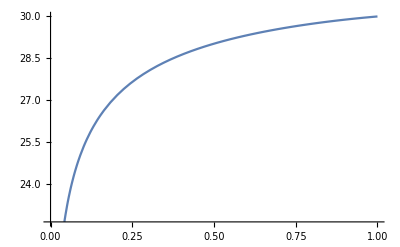

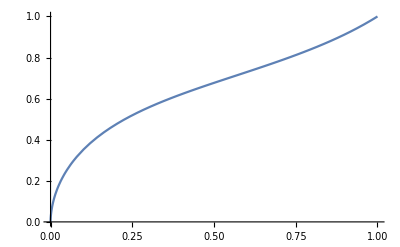

```mathematica
s=NDSolve[{eq1==0,eq2==0,a[1]==30,a'[1]==1,a'''[1]==1,b[1]==1,b'[1]==1},{a[r],b[r]},{r,0,1}]
Plot[Evaluate[{a[r],a'[r]}/. s],{r,0,1}]
Plot[Evaluate[{b[r],b'[r]}/. s],{r,0,1}]
```

```mathematica
ds1=eq1/.{b[r]->b,b'[r]->β,b''[r]->β',a[r]->a,a'[r]->α,a''[r]->α',a'''[r]->α''}
ds2=eq2/.{b[r]->b,b'[r]->β,b''[r]->β',a[r]->a,a'[r]->α,a''[r]->α',a'''[r]->α''}
```

-2 a b^2 α+3 a r^2 α β^2-(-2 a b^2 r+b^2 r^2 α) α'+β (-2 a b r α+b r^2 α^2-3 a b r^2 α')-a b r^2 α β'+a b^2 r^2 α''

-a^2 b^2+a^2 b^4-b^2 r^2 α^2-a b r^2 α β+3 a^2 r^2 β^2-a^2 b r^2 β'

```mathematica
ds1f=ds1/.{α->α,α'->A,α''->A'}
ds2f=ds2/.{α->α,α'->A,α''->A'}
```

-2 a b^2 α-A (-2 a b^2 r+b^2 r^2 α)+(-3 a A b r^2-2 a b r α+b r^2 α^2) β+3 a r^2 α β^2+a b^2 r^2 A'-a b r^2 α β'

-a^2 b^2+a^2 b^4-b^2 r^2 α^2-a b r^2 α β+3 a^2 r^2 β^2-a^2 b r^2 β'

```mathematica
FullSimplify[Solve[ds1f==0,A']]
FullSimplify[Solve[ds2f==0,β']]
```

{{A'→((2 b^2 (-A r+α))/r^2+b (3 A+(2 α)/r) β-3 α β^2+(b α (A b-α β))/a+b α β')/b^2}}

{{β'→-b/r^2+b^3/r^2-(b α^2)/a^2-(α β)/a+(3 β^2)/b}}

```mathematica
FullSimplify[Solve[ds1f==0,A']]
FullSimplify[%/.{β'->-b/r^2+b^3/r^2-(b α^2)/a^2-(α β)/a+(3 β^2)/b}]
```

{{A'→((2 b^2 (-A r+α))/r^2+b (3 A+(2 α)/r) β-3 α β^2+(b α (A b-α β))/a+b α β')/b^2}}

{{A'→-α^3/a^2+(α (A b-2 α β))/(a b)+(α (b+b^3+2 r β)+A r (-2 b+3 r β))/(b r^2)}}

```mathematica
a[r_]=Sum[Subscript[a, j]*r^j,{j,0,2}];
b[r_]=Sum[Subscript[b, j]*r^j,{j,0,2}];
Series[FullSimplify[eq1],{r,0,10}]
```

-2 (a_1^2 b_0^2) r+(-4 a_1 a_2 b_0^2-5 a_1^2 b_0 b_1) r^2+(-4 a_2^2 b_0^2-16 a_1 a_2 b_0 b_1-8 a_1^2 b_0 b_2) r^3+(-14 a_2^2 b_0 b_1+3 a_1^2 b_1 b_2-3 a_1 a_2 (b_1^2+10 b_0 b_2)) r^4+(-2 a_1 a_2 b_1 b_2+6 a_1^2 b_2^2-4 a_2^2 (b_1^2+6 b_0 b_2)) r^5+(-6 a_2^2 b_1 b_2+10 a_1 a_2 b_2^2) r^6+4 a_2^2 b_2^2 r^7+O[r]^11

```mathematica
Subscript[b, 0]=0;
Series[FullSimplify[eq1],{r,0,5}]
```

-a_0 a_1 b_1^2 r^2-4 (a_0 a_2 b_1^2) r^3+(-3 a_1 a_2 b_1^2+(3 a_1^2-10 a_0 a_2) b_1 b_2+4 a_0 a_1 b_2^2) r^4+(-4 a_2^2 b_1^2-2 a_1 a_2 b_1 b_2+6 a_1^2 b_2^2) r^5+O[r]^6

```mathematica
Subscript[a, 0]=0;
Series[FullSimplify[eq1],{r,0,5}]
```

(-3 a_1 a_2 b_1^2+3 a_1^2 b_1 b_2) r^4+(-4 a_2^2 b_1^2-2 a_1 a_2 b_1 b_2+6 a_1^2 b_2^2) r^5+O[r]^6

```mathematica
FullSimplify[Solve[-3 Subscript[a, 1] Subscript[a, 2] Subscript[b, 1]^2+3 Subscript[a, 1]^2 Subscript[b, 1] Subscript[b, 2]==0,Subscript[a, 2] ]]
```

{{a_2→(a_1 b_2)/b_1}}

```mathematica
Subscript[a, 2]=(Subscript[a, 1] Subscript[b, 2])/Subscript[b, 1];
Series[FullSimplify[eq2],{r,0,5}]
```

O[r]^6

```mathematica
a[r]
b[r]
```

r a_1+(r^2 a_1 b_2)/b_1

r b_1+r^2 b_2